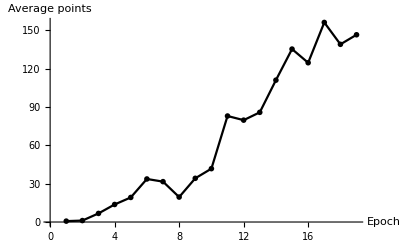

```mathematica
Import["/Users/cwalker32/Code/breakout_rl/deep_q_rl/results.csv"];
rewardper=Import["/Users/cwalker32/Code/breakout_rl/deep_q_rl/results.csv"][[2;;,4]];
meanq=Import["/Users/cwalker32/Code/breakout_rl/deep_q_rl/results.csv"][[2;;,5]];
rewardperplot=ListPlot[rewardper,PlotTheme->"Monochrome",LabelStyle->{FontFamily->"Times",FontSize->13,-Graphics-},Joined->True,AxesLabel->{"Epoch","Average points"}]
```

```mathematica
Export["/Users/cwalker32/Code/breakout_rl/presentation/dqn_rewardper.pdf",rewardperplot];
```

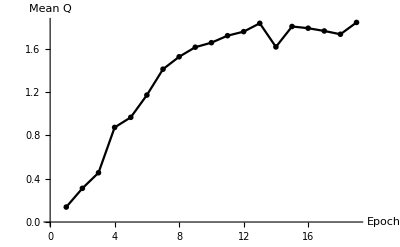

```mathematica
ListPlot[meanq,PlotTheme->"Monochrome",LabelStyle->{FontFamily->"Times",FontSize->13,-Graphics-},Joined->True,AxesLabel->{"Epoch","Mean Q"}]
```